```mathematica
βdec = √(nH Γ)Exp[-Γ/2 t]
```

ⅇ^(-(t Γ)/2) √(nH Γ)

```mathematica
Assuming[nH>0,Integrate[Abs[βdec]^2,{t,0,∞}]]
```

nH

```mathematica
βinc=(HeavisideTheta[t0-t] √Γ Exp[Γ/2(t-t0)])
```

ⅇ^(1/2 (t-t0) Γ) √Γ HeavisideTheta[-t+t0]

```mathematica
Assuming[t0>0,Integrate[Abs[βinc]^2,{t,0,∞}]]//cf
```

$Aborted

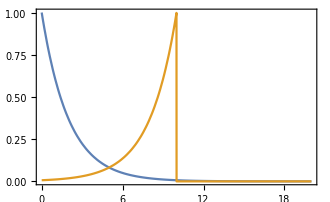

∫_0^∞ ⅇ^((t-t0) Γ) Γ Abs[HeavisideTheta[-t+t0]]^2ⅆt

```mathematica
Plot[{βdec/.nH->1/.Γ->1,βinc/.t0->10/.Γ->1},{t,0,20}]
```

```mathematica
Integrate[Abs[√Γ Exp[-Γ/2 t]]^2,{t,0,∞}]//cf
```

1